# Squarified Treemap

## A Functional Implementation in Mathematica

By Jeffrey Starr, 2014-02

## Abstract

This paper presents an implementation of the Squarified Treemap algorithm (originally published by Bruls, Huizing, and van Wijk)1 for multiple-levels of hierarchy written in a functional style using the Mathematica language.

## Introduction

A treemap is a popular visualization technique because of its density (high data content per square inch) and ability to handle hierarchical data. Treemaps visualize quantities by creating rectangles with areas that match (proportionally, at least) the original quantities. Viewers compare values by comparing areas. By using rectangles, treemaps are more dense than pie charts and there is evidence humans can compare areas of rectangles more accurately than wedges of a circle. Treemaps can also connote hierarchy by embedding rectangles in other rectangles recursively. This technique is often used to help viewers find files consuming excessive disk space by plotting the file size as the area of the rectangle and embedding the file rectangles within other rectangles to show the directory structure.2

## Rectangle, the Core Data Structure

The Squarified Treemap algorithm draws rectangles in other rectangles. Not all treemap algorithms use rectangles, but rectangles are the most popular choice.

Mathematica provides an existing data structure for a Rectangle which we will use within this paper.

```mathematica
?Rectangle
```

RowBox[{"Rectangle", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] is a two-dimensional graphics primitive that represents a filled rectangle, oriented parallel to the axes. 
RowBox[{"Rectangle", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}], "]"}] corresponds to a unit square with its bottom-left corner at RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]]}], "}"}].

Note that x and y refer to Cartesian coordinates, not screen coordinates. Beyond this data structure, we need several utility functions:

```mathematica
Coord[side_,Rectangle[{xmin_,ymin_},{xmax_,ymax_}]]:=
Switch[side,
Top,ymax,
Bottom,ymin,
Left,xmin,
Right,xmax]
```

```mathematica
Width[r_Rectangle]:=Abs[Coord[Right,r]-Coord[Left,r]]
```

```mathematica
Height[r_Rectangle]:=Abs[Coord[Top,r]-Coord[Bottom,r]]
```

```mathematica
Area[r_Rectangle]:=Width[r]×Height[r]
```

The aspect ratio of a rectangle is the proportion of the longest edge to the shorter edge (thus, the aspect ratio is always greater than or equal to one). For a degenerate rectangle (where either the height or width is zero), we will define the aspect ratio as infinite.

```mathematica
RectAspectRatio[r_Rectangle]:=
Which[
Width[r]==0∨Height[r]==0,∞,
Width[r]≥Height[r],Width[r]/Height[r],
Width[r]<Height[r],Height[r]/Width[r]
]
```

### Examples: Rectangle Functions

```mathematica
Block[
{r=Rectangle[{0,0},{6,4}]},
{Width[r],Height[r],Area[r],RectAspectRatio[r]}
]
```

{6,4,24,3/2}

## Sidebar: Visualization

The algorithm presented in this paper is independent of a graphical rendering system. However, as we generate rectangles, it is useful to see them plotted for verification. The function below takes a list of rectangles and plots them, with axes and a gridline, using Mathematica’s graphic capabilities.

```mathematica
VisualizeRectangles[rectangles_List]:=
Graphics[
Join[
{EdgeForm[{Thick,Black}],
Opacity[7/10]},
Riffle[rectangles,ColorData["Atoms","ColorList"]]
],
Axes->True,
GridLines->Automatic
]
```

As an example of the output:

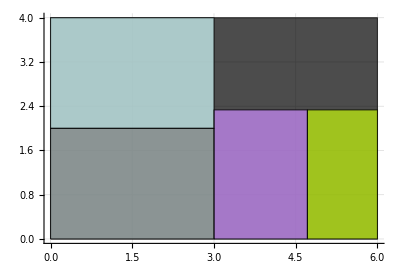

```mathematica
VisualizeRectangles[
{Rectangle[{0,0},{6,4}],
Rectangle[{0,0},{3,2}],
Rectangle[{0,2},{3,4}],
Rectangle[{3,0},{33/7,7/3}],
Rectangle[{33/7,0},{6,7/3}]}]
```

## Filling a Rectangle

Given a rectangle and a list of desired areas for sub-rectangles (the sum of those areas is equal to or less than the area of the parent rectangle), we can iteratively fill the parent rectangle with child rectangles. For the squarified treemap algorithm, we fill in rectangles either vertically (stack children on top of each other, flushed to the left) or horizontally (stack children to the right of each other, flush to the left and right edges and growing upwards).

In the vertical case, the height of each rectangle is proportional and scaled to the total areas of the children and the fixed height of the parent. Contrawise, in the horizontal case, the widths of each rectangles are proportional and scaled to the fixed width of the parent. Within these constraints, the width or height (respectively) can be computed using the child’s desired area.

### Fill Vertically

```mathematica
FillRectangle[parent_Rectangle,{},Vertical]:={}
```

```mathematica
FillRectangle[parent_Rectangle,areas_List,Vertical]:=
Block[
{heights=Prepend[Height[parent]*Accumulate[areas]/Total[areas],0]},
Table[
Rectangle[
{Coord[Left,parent],
Coord[Bottom,parent]+heights[[i]]},
{Coord[Left,parent]+areas[[i]]/(heights[[i+1]]-heights[[i]]),
Coord[Bottom,parent]+heights[[i+1]]}
],
{i,Length[heights]-1}
]
]
```

### Fill Horizontally

```mathematica
FillRectangle[parent_Rectangle,{},Horizontal]:={}
```

```mathematica
FillRectangle[parent_Rectangle,areas_List,Horizontal]:=
Block[
{widths=Prepend[Width[parent]*Accumulate[areas]/Total[areas],0]},
Table[
Rectangle[
{Coord[Left,parent]+widths[[i]],
Coord[Bottom,parent]},
{Coord[Left,parent]+widths[[i+1]],
Coord[Bottom,parent]+areas[[i]]/(widths[[i+1]]-widths[[i]])}
],
{i,Length[widths]-1}
]
]
```

### Examples: Fill Horizontally and Vertically

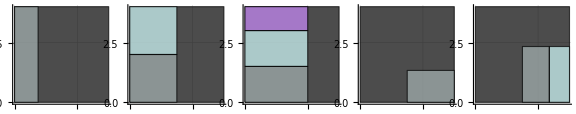

```mathematica
Block[
{parent=Rectangle[{0,0},{6,4}],
p2=Rectangle[{3,0},{6,4}]},
GraphicsRow[
{VisualizeRectangles[Join[{parent},FillRectangle[parent,{6},Vertical]]],
VisualizeRectangles[
Join[{parent},FillRectangle[parent,{6,6},Vertical]]],
VisualizeRectangles[
Join[{parent},FillRectangle[parent,{6,6,4},Vertical]]],
VisualizeRectangles[
Join[{parent},FillRectangle[p2,{4},Horizontal]]],
VisualizeRectangles[
Join[{parent},FillRectangle[p2,{4,3},Horizontal]]]
},
ImageSize->Large,
Spacings->0
]
]
```

## How Many Children?

We can add all children to a rectangle using the same orientation. However, this leads to narrow rectangles that hard to compare:

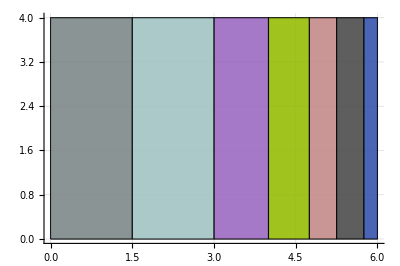

```mathematica
Block[
{parent=Rectangle[{0,0},{6,4}]},
VisualizeRectangles[
Join[{parent},FillRectangle[parent,{6,6,4,3,2,2,1},Horizontal]]
]
]
```

The squarified treemap algorithm uses a heuristic to first fill a rectangle with children using one orientation, then switch to the opposite orientation, and so on. The algorithm places a child rectangles until the worst aspect ratio of the group of placed rectangles increases. In other words, rectangles are placed until a local minima of the aspect ratio is found. The worst aspect ratio is simply the maximum aspect ratio of a list. If the list is empty, we define the worst aspect ratio as infinite.

```mathematica
WorstAspectRatio[{}]:=∞
```

```mathematica
WorstAspectRatio[rectangles_List]:=
Max[RectAspectRatio[#]&/@rectangles]
```

```mathematica
PlaceTillLocalMinima[parent_Rectangle,areas_List,orientation_]:=
PlaceTillLocalMinima[parent,areas,orientation,{}]
```

The PlaceTillLocalMinima (4 argument) function takes a parent rectangle, a list of desired areas for child rectangles, an orientation (either Vertical or Horizontal), and accumulates a list of rectangles placed using FillRectangle.

```mathematica
PlaceTillLocalMinima[parent_Rectangle,areas_List,orientation_,placed_List]:=
If[Length[placed]==Length[areas],placed (* local minima achieved *),
Block[
{placeStep=FillRectangle[parent,Take[areas,Length[placed]+1],orientation]},
If[WorstAspectRatio[placeStep]>WorstAspectRatio[placed],
placed(*previous step had local minima*),
PlaceTillLocalMinima[parent,areas,orientation,placeStep](*recurse and check if next step is local minima*)
]
]
]
```

When a local minima is found, the upper-level function will place the remaining children using the opposite orientation. This function provides the flip:

```mathematica
InvertOrientation[Horizontal]:=Vertical
```

```mathematica
InvertOrientation[Vertical]:=Horizontal
```

### Examples: Finding Local Minima

The function finds that placing just the first two rectangles reaches the local minima:

```mathematica
PlaceTillLocalMinima[Rectangle[{0,0},{6,4}],{6,6,4,3,2,2,1},Vertical]
```

{Rectangle[{0,0},{3,2}],Rectangle[{0,2},{3,4}]}

```mathematica
WorstAspectRatio[%]
```

3/2

The worst aspect ratio for the next step (placing 6, 6, and 4) is 4, which is greater than 3/2.

```mathematica
WorstAspectRatio[FillRectangle[Rectangle[{0,0},{6,4}],{6,6,4},Vertical]]
```

4

Similarly, the function finds the local minima after the first two rectangles:

```mathematica
PlaceTillLocalMinima[Rectangle[{3,0},{6,4}],{4,3,2,1,1},Horizontal]
```

{Rectangle[{3,0},{33/7,7/3}],Rectangle[{33/7,0},{6,7/3}]}

```mathematica
WorstAspectRatio[%]
```

49/27

The worst aspect ratio for the next step (4, 3, and 2) is 9/2, which is greater than 49/27.

```mathematica
WorstAspectRatio[FillRectangle[Rectangle[{3,0},{6,4}],{4,3,2},Horizontal]]
```

9/2

## Calculating Remaining Dimensions

After the algorithm has placed a number of children, it will invert orientation and place the remaining children. The parent rectangle for the first group of children is different than the second group (and the third and fourth...) because some of the space has already been consumed. These pair of functions are used to calculate the “new” parent rectangle for the next iteration of rectangle placing.

First, given a group of placed rectangles, we need to find the bounding box around them. Due to the algorithm’s design, the bounding box will always be a rectangle flush with the child rectangles.

```mathematica
EnclosingRectangle[rectangles_List]:=
Rectangle[
{Min[Coord[Left,#]&/@rectangles],
Min[Coord[Bottom,#]&/@rectangles]},
{Max[Coord[Right,#]&/@rectangles],
Max[Coord[Top,#]&/@rectangles]}
]
```

Second, the remaining rectangle is formed from the right edge of the child (if the children were placed Vertically) or from the top edge of the child (if the children were placed Horizontally). The top-right corner is always equal to the parent.

```mathematica
RemainingRectangle[parent_Rectangle,child_Rectangle]:=
Rectangle[
{If[Coord[Bottom,parent]==Coord[Bottom,child]∧Coord[Top,parent]==Coord[Top,child],
Coord[Right,child],
(*else*)Coord[Left,parent]],
If[Coord[Left,parent]==Coord[Left,child]∧Coord[Right,parent]==Coord[Right,child],
Coord[Top,child],
(*else*)Coord[Bottom,parent]
]
},
{Coord[Right,parent],
Coord[Top,parent]}
]
```

### Examples: Remaining Rectangle

```mathematica
EnclosingRectangle[{Rectangle[{0,0},{3,2}],Rectangle[{0,2},{3,4}]}]
```

Rectangle[{0,0},{3,4}]

```mathematica
RemainingRectangle[
Rectangle[{0,0},{6,4}],
Rectangle[{0,0},{3,4}]]
```

Rectangle[{3,0},{6,4}]

```mathematica
RemainingRectangle[Rectangle[{3,0},{6,4}],EnclosingRectangle[{Rectangle[{3,0},{33/7,7/3}],Rectangle[{33/7,0},{6,7/3}]}]]
```

Rectangle[{3,7/3},{6,4}]

```mathematica
RemainingRectangle[Rectangle[{0,0},{1,1}],Rectangle[{0,0},{1,1}]]
```

Rectangle[{1,1},{1,1}]

## Squarify Algorithm

With all the pieces together, we can now write the Squarify function. This function takes a parent rectangle and a list of areas (whose sum must equal the area of the parent) and returns a list of Rectangles.

```mathematica
Squarify[parent_Rectangle,areas_List]:=
Squarify[parent,areas,{},Vertical]
```

```mathematica
Squarify[parent_Rectangle,areas_List,placed_List,orientation_]:=
If[Length[areas]==0,placed(*done*),
Block[
{placeThisStep=PlaceTillLocalMinima[parent,areas,orientation]},
Squarify[
RemainingRectangle[parent,EnclosingRectangle[placeThisStep]],
Drop[areas,Length[placeThisStep]],
Join[placed,placeThisStep],
InvertOrientation[orientation]
]
]
]
```

### Example: Squarify

```mathematica
Squarify[Rectangle[{0,0},{6,4}],{6,6,4,3,2,2,1}]
```

{Rectangle[{0,0},{3,2}],Rectangle[{0,2},{3,4}],Rectangle[{3,0},{33/7,7/3}],Rectangle[{33/7,0},{6,7/3}],Rectangle[{3,7/3},{21/5,4}],Rectangle[{21/5,7/3},{6,31/9}],Rectangle[{21/5,31/9},{6,4}]}

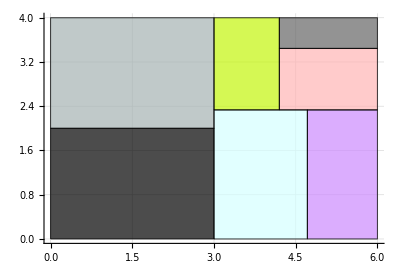

```mathematica
VisualizeRectangles[%]
```

## Squarify with Hierarchy

The version of Squarify defined in the previous section recursively breaks a rectangle into multiple subrectangles given a single list (layer) of areas. However, the original goal of treemaps was to show multiple layers of hierarchy -- demonstrate the concepts of membership and scale simultaneously.

### Encoding Hierarchy

In order to encode hierarchy, we will expand our earlier areas list into lists of lists. areas is a list consisting of either positive numbers or lists. If a list, that list may contain either positive numbers or lists. The sum of numbers in all the lists should be equal to or less than the area of the parent rectangle.

For example, the list hierarchicalData will serve as an example.

```mathematica
hierarchicalData={{4,3,2},{6,5},{{7},{9,8}}};
```

```mathematica
Total[hierarchicalData,∞]
```

44

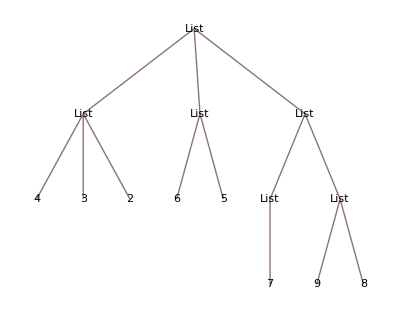

```mathematica
TreeForm[hierarchicalData]
```

### Extending Squarify

Given a list of areas, BaseLayerQ returns True if all the elements are numbers (and therefore Squarify can be used to layout the rectangle).

```mathematica
BaseLayerQ[areas_List]:=And@@(NumberQ[#]&/@areas)
```

```mathematica
BaseLayerQ[{3,4,5}]
```

True

```mathematica
BaseLayerQ[{{4},{5}}]
```

False

ChildArea returns the size of each child in the list, where a child may be either a number or a list (itself possibly containing may sub-lists).

```mathematica
ChildArea[areas_List]:=
If[NumberQ[First[areas]],
areas,
Total[#,∞]&/@areas
]
```

```mathematica
ChildArea[hierarchicalData]
```

{9,11,24}

```mathematica
ChildArea[{9,8}]
```

{9,8}

SquarifyHierarchy works by recursively processing the top-level areas list in depth-first search manner. For each layer, the function first tests to see if this layer does not have children using the BaseLayerQ function. If it does not, then the function calls Squarify. Otherwise, since the layer has children, Squarify is called with areas generated by ChildArea. The resulting list of rectangles can be recursively processed with their children.

```mathematica
SquarifyHierarchy[parent_Rectangle,areas_List]:=
If[Length[areas]==0,
(*nothing more to do*)
{},
(*else, more areas to process*)
If[BaseLayerQ[areas],
Squarify[parent,areas],
Block[
{immediateChildRectangles=Squarify[parent,ChildArea[areas]]},
Join[
immediateChildRectangles,
Flatten[Table[
SquarifyHierarchy[immediateChildRectangles[[i]],areas[[i]]],
{i,Length[areas]}
]
]
]
]
]
]
```

#### Example: SquarifyHierarchy

```mathematica
SquarifyHierarchy[Rectangle[{0,0},{6,4}],{6,6,4,3,2,2,1}]
```

{Rectangle[{0,0},{3,2}],Rectangle[{0,2},{3,4}],Rectangle[{3,0},{33/7,7/3}],Rectangle[{33/7,0},{6,7/3}],Rectangle[{3,7/3},{21/5,4}],Rectangle[{21/5,7/3},{6,31/9}],Rectangle[{21/5,31/9},{6,4}]}

```mathematica
SquarifyHierarchy[Rectangle[{0,0},{Sqrt[44],Sqrt[44]}],hierarchicalData]
```

{Rectangle[{0,0},{10/(√11),(9 √11)/10}],Rectangle[{0,(9 √11)/10},{10/(√11),2 √11}],Rectangle[{10/(√11),0},{2 √11,24/(-10/(√11)+2 √11)}],Rectangle[{0,0},{70/(9 √11),(18 √11)/35}],Rectangle[{0,(18 √11)/35},{70/(9 √11),(9 √11)/10}],Rectangle[{70/(9 √11),0},{10/(√11),(9 √11)/10}],Rectangle[{0,(9 √11)/10},{10/(√11),(3 √11)/2}],Rectangle[{0,(3 √11)/2},{10/(√11),2 √11}],Rectangle[{10/(√11),0},{2 √11,7/(-10/(√11)+2 √11)}],Rectangle[{10/(√11),7/(-10/(√11)+2 √11)},{2 √11,24/(-10/(√11)+2 √11)}],Rectangle[{10/(√11),0},{2 √11,7/(-10/(√11)+2 √11)}],Rectangle[{10/(√11),7/(-10/(√11)+2 √11)},{2 √11,16/(-10/(√11)+2 √11)}],Rectangle[{10/(√11),16/(-10/(√11)+2 √11)},{2 √11,24/(-10/(√11)+2 √11)}]}

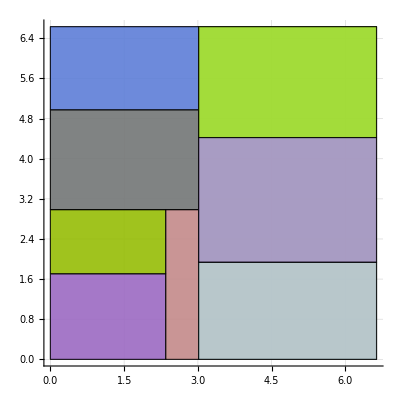

```mathematica
VisualizeRectangles[%]
```

## Dealing with User Data

### Cleaning Data

User data may include values that cannot be represented within a treemap (e.g. negative numbers). The function CleanData removes values from a hierarchy that cannot be represented, as well as returning lists of numbers in sorted order (descending). The later change is based on the original paper’s assertion that descending order for numbers produces the most aesthetic results.

```mathematica
ValidNonBaseLayerQ[areas_List]:=VectorQ[areas,ListQ]
```

```mathematica
ValidNonBaseLayerQ[{{3,4},{5,6,7}}]
```

True

```mathematica
ValidNonBaseLayerQ[{3,4}]
```

False

```mathematica
CleanData[areas_List]:=
Which[
BaseLayerQ[areas],
Sort[Select[areas,#>0&],Greater],
ValidNonBaseLayerQ[areas],
CleanData[#]&/@areas,
True,
Abort[]
]
```

```mathematica
CleanData[hierarchicalData]
```

{{4,3,2},{6,5},{{7},{9,8}}}

```mathematica
CleanData[{{2,3,-1,4},{6,5},{7},{8,9,0}}]
```

{{4,3,2},{6,5},{7},{9,8}}

Treemap is a wrapper around SquarifyHierarchy that first filters a list of values using CleanData. Then, Treemap scales the values to the area of the parent rectangle (a rectangle with width and height provided as parameters). The result is returned as a graphic objects generated via VisualizeRectangles.

```mathematica
Treemap[width_Integer,height_Integer,values_List]:=
Block[
{safeValues=CleanData[values],
parentArea=width*height},
VisualizeRectangles[
SquarifyHierarchy[
Rectangle[{0,0},{width,height}],
safeValues*(parentArea/Total[safeValues,∞])
]
]
]
```

### Example: Treemap

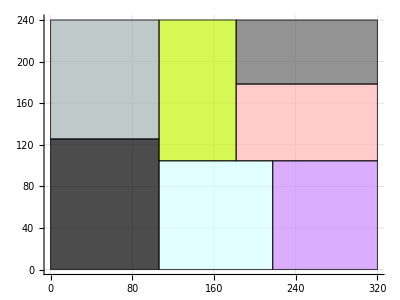

```mathematica
Treemap[320,240,{858,1020,1119,715,976,857,900}]
```

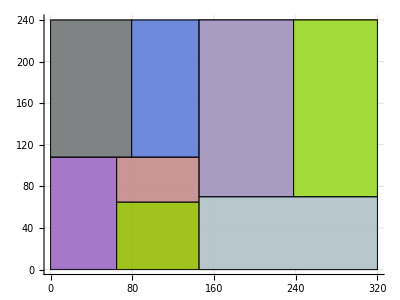

```mathematica
Treemap[320,240,hierarchicalData]
```

## References

1	M. Bruls, K. Huizing, and J. van Wijk, "Squarified treemaps," in Proceedings of the Joint Eurographics and IEEE TCVG Symposium on Visualization, pp. 33-42, 2000.

2	http://en.wikipedia.org/wiki/File:Tree_Map.png